# VO Modelling in Evolutionary Biology

## Exercises

### Simplifications

#### 1.)

```mathematica
Simplify[((a x)^2-a^2)/(a x-a)]
```

a (1+x)

#### 3.)

```mathematica
Simplify[Log[a]+Log[x]+Log[b]+Log[x]-Log[c]]
```

Log[a]+Log[b]-Log[c]+2 Log[x]

#### 5.)

```mathematica
Sum[1,{n,1,x}]
```

x

### Equations

#### 7.)

```mathematica
Solve[2 x^2-7 x+3==0,x]
```

{{x→1/2},{x→3}}

#### 11.)

```mathematica
Solve[x^3-y x^2==x-y,x]
```

{{x→-1},{x→1},{x→y}}

#### 12.)

```mathematica
Solve[Log[(a^x)]==1/2,x]
```

{{x→1/(2 Log[a])}}

#### 13.)

```mathematica
Solve[a^(r*x)==100,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Log[100]/(r Log[a])}}

### Inequalities

#### 14.)

```mathematica
FindInstance[-x/3+5>15,x]
```

{{x→-31}}

#### 16.)

```mathematica
FindInstance[(x+3)/2<(x+2)/-3,x]
```

{{x→-14/5}}

### Derivatives

#### 19.)

```mathematica
f[x_] := ⅇ^(3 x)
```

```mathematica
f'[x]
```

3 ⅇ^(3 x)

#### 24.)

```mathematica
g[x_] := Log[(a x^2)]
```

```mathematica
g'[x]//MatrixForm
```

2/x

```mathematica
D[(Log[(b x^2)]),x]//MatrixForm
```

2/x

```mathematica
D[b x^2,x]
```

2 b x

```mathematica
n={1,2,3,4,5,6,7,8,9}
```

{1,2,3,4,5,6,7,8,9}

```mathematica
Expand[(x-e)^n]//MatrixForm
```

(-e+x
e^2-2 e x+x^2
-e^3+3 e^2 x-3 e x^2+x^3
e^4-4 e^3 x+6 e^2 x^2-4 e x^3+x^4
-e^5+5 e^4 x-10 e^3 x^2+10 e^2 x^3-5 e x^4+x^5
e^6-6 e^5 x+15 e^4 x^2-20 e^3 x^3+15 e^2 x^4-6 e x^5+x^6
-e^7+7 e^6 x-21 e^5 x^2+35 e^4 x^3-35 e^3 x^4+21 e^2 x^5-7 e x^6+x^7
e^8-8 e^7 x+28 e^6 x^2-56 e^5 x^3+70 e^4 x^4-56 e^3 x^5+28 e^2 x^6-8 e x^7+x^8
-e^9+9 e^8 x-36 e^7 x^2+84 e^6 x^3-126 e^5 x^4+126 e^4 x^5-84 e^3 x^6+36 e^2 x^7-9 e x^8+x^9)

```mathematica
poly[n_]:=(temp=0;While[n>temp,temp=(temp+2)];temp)
```

```mathematica
poly[13]
```

14

```mathematica
Integrate[ⅇ^-(r x),x]
```

-ⅇ^(-r x)/r

```mathematica
Limit[(x^4-4)/(x^3-1),x->1]
```

-∞

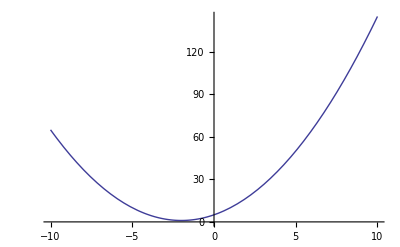

```mathematica
Plot[x^2+4 x+5,{x,-10,10}]
```